Start with a Gaussian blob of integral 1.

{A>0,B>0,r>0,ϵ>0,α∈Complexes}

(ⅇ^(-r^2/ϵ^2))/(π^(3/2) ϵ^3)

-(2 ⅇ^(-r^2/ϵ^2) r)/(π^(3/2) ϵ^5)

-2/(π^(3/2) ϵ^5)

1

(-2 ⅇ^(-r^2/ϵ^2) r+√π ϵ Erf[r/ϵ])/(4 π^(3/2) r^2 ϵ)

G'/r and limit at r=0

(-(2 ⅇ^(-r^2/ϵ^2) r)/ϵ+√π Erf[r/ϵ])/(4 π^(3/2) r^3)

1/(3 π^(3/2) ϵ^3)

-Erf[r/ϵ]/(4 π r)

-1/(2 π^(3/2) ϵ)

Get the Green's function

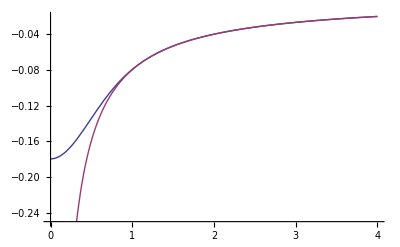

```mathematica
TextCell["Start with a Gaussian blob of integral 1."]
Clear[A,B,C1,C2,C3,C4,α,ϵ,r,Gp,Ge,Be,f1,f2,ϕ,H1,H2]
$Assumptions={A>0,B>0,r>0,ϵ>0,α∈Complexes}
 ϕ[r_] := 1/Pi^(3/2)/ϵ^3*Exp[-r^2/ϵ^2] 
ϕ[r]
D[ϕ[r],r]
Limit[D[ϕ[r],r]/r,r->0]
Integrate[4*Pi*r^2*ϕ[r],{r,0,Infinity}]
Gp[r_] = (Integrate[r^2*ϕ[r],r] + 0)/r^2
Text["G'/r and limit at r=0"]
FullSimplify[Gp[r]/r]
Limit[Gp[r]/r,r->0]
Ge[r_] = Integrate[Gp[r],r] 
Limit[Ge[r],r->0]
TextCell["Get the Green's function"]
Ge[r]/.ϵ->1/2;
Plot[{%,-1/(4*Pi*r)},{r,0,4}]
```

```mathematica
TextCell["Now we find Be using the integrals from my thesis. Here is Be."]
f1[r_] := (Exp[-α*r]/r)*(C1-(1/(2*α))*Integrate[r*Exp[α*r]*Ge[r],r])
f2[r_] := (Exp[α*r]/r)*(C2+(1/(2*α))*Integrate[r*Exp[-α*r]*Ge[r],r])
Be[r_]:=f1[r]+f2[r]
Be[r]
TextCell["Check that Be[r] satisfies the PDE"]
Simplify[D[D[Be[r],r],r]+2/r*D[Be[r],r] - α^2*Be[r] - Ge[r]]
```

Now we find Be using the integrals from my thesis. Here is Be.

(ⅇ^(-r α) (C1+(ⅇ^(r α) Erf[r/ϵ]-ⅇ^((α^2 ϵ^2)/4) Erf[r/ϵ-(α ϵ)/2])/(8 π α^2)))/r+(ⅇ^(r α) (C2-(-ⅇ^(-r α) Erf[r/ϵ]+ⅇ^((α^2 ϵ^2)/4) Erf[r/ϵ+(α ϵ)/2])/(8 π α^2)))/r

Check that Be[r] satisfies the PDE

0

```mathematica
TextCell["Do an expansion at r -> Infinity for the difference between the regularized Be and the singular B."]
tmp1=Collect[Normal[Series[Be[r],{r,Infinity,0}]]-(1-Exp[-α*r])/(4*Pi*α^2*r),Exp[α*r]]
TextCell["Do an expansion at r =0 to keep it bounded."]
tmp2=Normal[Series[Be[r],{r,0,0}]]
```

Do an expansion at r -> Infinity for the difference between the regularized Be and the singular B.

ⅇ^(r α) (C2/r-(ⅇ^((α^2 ϵ^2)/4))/(8 π r α^2))+ⅇ^(-r α) (C1/r+1/(4 π r α^2)-(ⅇ^((α^2 ϵ^2)/4))/(8 π r α^2))

Do an expansion at r =0 to keep it bounded.

(C1+C2)/r-C1 α+C2 α-(ⅇ^((α^2 ϵ^2)/4) Erf[(α ϵ)/2])/(4 π α)

```mathematica
TextCell["Make the positive exponential in the infinite limit vanish."]
ans2 = Solve[Take[tmp1,1]==0,C2]
C2=C2/.ans2[[1]];
TextCell["Make the 1/r term at the 0 limit vanish."]
ans1 = Solve[Take[tmp2,1]==0,C1]
C1 = C1/.ans1[[1]];
```

Make the positive exponential in the infinite limit vanish.

{{C2→(ⅇ^((α^2 ϵ^2)/4))/(8 π α^2)}}

Make the 1/r term at the 0 limit vanish.

{{C1→-(ⅇ^((α^2 ϵ^2)/4))/(8 π α^2)}}

Check the expansion at r=infinity to verify decay to exact solution.

1/(4 π r α^2)-(ⅇ^(-r α+(α^2 ϵ^2)/4))/(4 π r α^2)

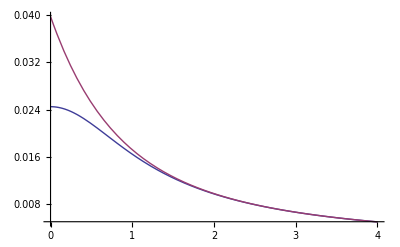

```mathematica
TextCell["Check the expansion at r=infinity to verify decay to exact solution."]
Collect[Normal[Series[Be[r],{r,Infinity,0}]],Exp[α*r]]
Be[r]/.{ϵ->1/2,α->2};
Plot[{%,(1-Exp[-2*r])/(4*Pi*2^2*r)},{r,0,4}]
```

```mathematica
Limit[Be[r],ϵ->0]
```

-(-1+ⅇ^(-r α))/(4 π r α^2)

```mathematica
TextCell["Final Be."]
Be[r]
TextCell["Calculate the H1 and H2 functions. H1:"]
H1 = Collect[Simplify[-D[Be[r],{r,2}] - D[Be[r],r]/r],Exp[2rα]]
TextCell["H2:"]
H2 = Simplify[D[Be[r],{r,2}]/r^2 - D[Be[r],r]/r^3]
```

Final Be.

(ⅇ^(-r α) (-(ⅇ^((α^2 ϵ^2)/4))/(8 π α^2)+(ⅇ^(r α) Erf[r/ϵ]-ⅇ^((α^2 ϵ^2)/4) Erf[r/ϵ-(α ϵ)/2])/(8 π α^2)))/r+(ⅇ^(r α) ((ⅇ^((α^2 ϵ^2)/4))/(8 π α^2)-(-ⅇ^(-r α) Erf[r/ϵ]+ⅇ^((α^2 ϵ^2)/4) Erf[r/ϵ+(α ϵ)/2])/(8 π α^2)))/r

Calculate the H1 and H2 functions. H1:

1/(8 π r^3 α^2)ⅇ^(-r α) (-2 ⅇ^(r α) Erf[r/ϵ]+ⅇ^((α^2 ϵ^2)/4) (1-ⅇ^(2 r α)+r α+ⅇ^(2 r α) r α+r^2 α^2-ⅇ^(2 r α) r^2 α^2+(1+r α+r^2 α^2) Erf[r/ϵ-(α ϵ)/2]+ⅇ^(2 r α) (1-r α+r^2 α^2) Erf[r/ϵ+(α ϵ)/2]))

H2:

-1/(8 π r^5 α^2)ⅇ^(-r α) (-6 ⅇ^(r α) Erf[r/ϵ]+ⅇ^((α^2 ϵ^2)/4) (3-3 ⅇ^(2 r α)+3 r α+3 ⅇ^(2 r α) r α+r^2 α^2-ⅇ^(2 r α) r^2 α^2+(3+3 r α+r^2 α^2) Erf[r/ϵ-(α ϵ)/2]+ⅇ^(2 r α) (3-3 r α+r^2 α^2) Erf[r/ϵ+(α ϵ)/2]))

```mathematica
Limit[H1,ϵ -> 0]
```

(ⅇ^(-r α) (1-ⅇ^(r α)+r α+r^2 α^2))/(4 π r^3 α^2)

```mathematica
Limit[H2,ϵ->0]
```

(ⅇ^(-r α) (-3+3 ⅇ^(r α)-3 r α-r^2 α^2))/(4 π r^5 α^2)

```mathematica
Limit[H1,r->0]
Limit[H2,r->0]
```

(2/π^(3/2)-(ⅇ^((α^2 ϵ^2)/4) α ϵ)/π+(ⅇ^((α^2 ϵ^2)/4) α ϵ Erf[(α ϵ)/2])/π)/(6 ϵ)

(4-2 α^2 ϵ^2+ⅇ^((α^2 ϵ^2)/4) √π α^3 ϵ^3-ⅇ^((α^2 ϵ^2)/4) √π α^3 ϵ^3 Erf[(α ϵ)/2])/(60 π^(3/2) ϵ^3)

```mathematica
TextCell["Check the expansion at r=infinity to see decay rate."]
s1 = Collect[Normal[Series[H1,{r,Infinity,6}]],Exp[-α*r]];
t1 = Simplify[Take[s1,1]];
t2 = Expand[Take[s1,{2,2}]];
t1+t2
```

Check the expansion at r=infinity to see decay rate.

-1/(4 π r^3 α^2)+(ⅇ^(1/4 α (-4 r+α ϵ^2)) (1+r α+r^2 α^2))/(4 π r^3 α^2)-(ⅇ^(-r^2/ϵ^2) ϵ)/(4 π^(3/2) r^2)-(ⅇ^(-r^2/ϵ^2) ϵ^3)/(8 π^(3/2) r^6 α^2)-(ⅇ^(-r^2/ϵ^2) α^2 ϵ^5)/(16 π^(3/2) r^4)

```mathematica
Clear[s1,t1,t2]
TextCell["Check the expansion at r=infinity to see decay rate."]
s1 = Collect[Normal[Series[H2,{r,Infinity,8}]],Exp[-α*r]];
t1 = Simplify[Take[s1,1]];
t2 = Expand[Take[s1,{2,2}]];
t1+t2
```

Check the expansion at r=infinity to see decay rate.

3/(4 π r^5 α^2)-(ⅇ^(1/4 α (-4 r+α ϵ^2)) (3+3 r α+r^2 α^2))/(4 π r^5 α^2)+(ⅇ^(-r^2/ϵ^2) ϵ)/(4 π^(3/2) r^4)+(ⅇ^(-r^2/ϵ^2) ϵ^3)/(4 π^(3/2) r^6)+(3 ⅇ^(-r^2/ϵ^2) ϵ^3)/(8 π^(3/2) r^8 α^2)+(ⅇ^(-r^2/ϵ^2) α^2 ϵ^5)/(16 π^(3/2) r^6)

```mathematica
TextCell["Experiments in integrating"]
(*$Assumptions={a>0}
H1tmp = H1/.r->Sqrt[a*s^2+b*s+c];
Integrate[s*H1tmp,s]*)
```

Experiments in integrating

```mathematica
tmp1=Collect[Expand[H1],Erf[r/ϵ]]
```

(ⅇ^(-r α+(α^2 ϵ^2)/4))/(8 π r)-(ⅇ^(r α+(α^2 ϵ^2)/4))/(8 π r)+(ⅇ^(-r α+(α^2 ϵ^2)/4))/(8 π r^3 α^2)-(ⅇ^(r α+(α^2 ϵ^2)/4))/(8 π r^3 α^2)+(ⅇ^(-r α+(α^2 ϵ^2)/4))/(8 π r^2 α)+(ⅇ^(r α+(α^2 ϵ^2)/4))/(8 π r^2 α)-Erf[r/ϵ]/(4 π r^3 α^2)+(ⅇ^(-r α+(α^2 ϵ^2)/4) Erf[r/ϵ-(α ϵ)/2])/(8 π r)+(ⅇ^(-r α+(α^2 ϵ^2)/4) Erf[r/ϵ-(α ϵ)/2])/(8 π r^3 α^2)+(ⅇ^(-r α+(α^2 ϵ^2)/4) Erf[r/ϵ-(α ϵ)/2])/(8 π r^2 α)+(ⅇ^(r α+(α^2 ϵ^2)/4) Erf[r/ϵ+(α ϵ)/2])/(8 π r)+(ⅇ^(r α+(α^2 ϵ^2)/4) Erf[r/ϵ+(α ϵ)/2])/(8 π r^3 α^2)-(ⅇ^(r α+(α^2 ϵ^2)/4) Erf[r/ϵ+(α ϵ)/2])/(8 π r^2 α)

```mathematica
Expand[H1];
tmp1=Collect[Expand[H1],Erf[r/ϵ]]
(*$Assumptions={a>0}
tmp2=tmp1/. r->Sqrt[a*s^2+b*s+c]
Integrate[tmp2,s]
Integrate[tmp2,{s,0,1}]*)
```

(ⅇ^(-r α+(α^2 ϵ^2)/4))/(8 π r)-(ⅇ^(r α+(α^2 ϵ^2)/4))/(8 π r)+(ⅇ^(-r α+(α^2 ϵ^2)/4))/(8 π r^3 α^2)-(ⅇ^(r α+(α^2 ϵ^2)/4))/(8 π r^3 α^2)+(ⅇ^(-r α+(α^2 ϵ^2)/4))/(8 π r^2 α)+(ⅇ^(r α+(α^2 ϵ^2)/4))/(8 π r^2 α)-Erf[r/ϵ]/(4 π r^3 α^2)+(ⅇ^(-r α+(α^2 ϵ^2)/4) Erf[r/ϵ-(α ϵ)/2])/(8 π r)+(ⅇ^(-r α+(α^2 ϵ^2)/4) Erf[r/ϵ-(α ϵ)/2])/(8 π r^3 α^2)+(ⅇ^(-r α+(α^2 ϵ^2)/4) Erf[r/ϵ-(α ϵ)/2])/(8 π r^2 α)+(ⅇ^(r α+(α^2 ϵ^2)/4) Erf[r/ϵ+(α ϵ)/2])/(8 π r)+(ⅇ^(r α+(α^2 ϵ^2)/4) Erf[r/ϵ+(α ϵ)/2])/(8 π r^3 α^2)-(ⅇ^(r α+(α^2 ϵ^2)/4) Erf[r/ϵ+(α ϵ)/2])/(8 π r^2 α)

```mathematica
Integrate[Erf[r]/r^3,r]
```

-(ⅇ^(-r^2))/(√π r)-Erf[r]-Erf[r]/(2 r^2)

```mathematica
(* Find the associated dipole *)
Q1 =Collect[Collect[FullSimplify[Expand[D[D[H1,r],r]+2*D[H1,r]/r + 2*H2]],(1+r α (-1+r α))],(1+r α (1+r α))]
Q2 = Collect[Collect[FullSimplify[Expand[D[D[H2,r],r]+6*D[H2,r]/r] ],(3+r α (-3+r α))],(3+r α (3+r α))]
c = -(H2 /. r -> a)/(Q2 /. r -> a)
```

-(ⅇ^(r α-r (α+r/ϵ^2)) (2 r^2+ϵ^2))/(2 π^(3/2) r^2 ϵ^3)-(ⅇ^(-r (α+r/ϵ^2)+r^2/ϵ^2+(α^2 ϵ^2)/4) (1+r α (1+r α)) (-2+Erfc[r/ϵ-(α ϵ)/2]))/(8 π r^3)-(ⅇ^(2 r α-r (α+r/ϵ^2)+r^2/ϵ^2+(α^2 ϵ^2)/4) (1+r α (-1+r α)) Erfc[r/ϵ+(α ϵ)/2])/(8 π r^3)

(ⅇ^(r α-r (α+r/ϵ^2)) (2 r^2+3 ϵ^2))/(2 π^(3/2) r^4 ϵ^3)+(ⅇ^(-r (α+r/ϵ^2)+r^2/ϵ^2+(α^2 ϵ^2)/4) (3+r α (3+r α)) (-2+Erfc[r/ϵ-(α ϵ)/2]))/(8 π r^5)+(ⅇ^(2 r α-r (α+r/ϵ^2)+r^2/ϵ^2+(α^2 ϵ^2)/4) (3+r α (-3+r α)) Erfc[r/ϵ+(α ϵ)/2])/(8 π r^5)

(ⅇ^(-a α) (-6 ⅇ^(a α) Erf[a/ϵ]+ⅇ^((α^2 ϵ^2)/4) (3-3 ⅇ^(2 a α)+3 a α+3 a ⅇ^(2 a α) α+a^2 α^2-a^2 ⅇ^(2 a α) α^2+(3+3 a α+a^2 α^2) Erf[a/ϵ-(α ϵ)/2]+ⅇ^(2 a α) (3-3 a α+a^2 α^2) Erf[a/ϵ+(α ϵ)/2])))/(8 a^5 π α^2 ((ⅇ^(a α-a (α+a/ϵ^2)) (2 a^2+3 ϵ^2))/(2 a^4 π^(3/2) ϵ^3)+(ⅇ^(-a (α+a/ϵ^2)+a^2/ϵ^2+(α^2 ϵ^2)/4) (3+a α (3+a α)) (-2+Erfc[a/ϵ-(α ϵ)/2]))/(8 a^5 π)+(ⅇ^(2 a α-a (α+a/ϵ^2)+a^2/ϵ^2+(α^2 ϵ^2)/4) (3+a α (-3+a α)) Erfc[a/ϵ+(α ϵ)/2])/(8 a^5 π)))

```mathematica
(* Explore erf *)
Erf[1.0+I]
Erfc[1.0+I]
1-Erf[1.0+I]
```

1.31615+0.190453 ⅈ

-0.316151-0.190453 ⅈ

-0.316151-0.190453 ⅈ

```mathematica
Limit[Q1,r->0]
Limit[Q2,r->0]
```

(-4+2 α^2 ϵ^2-ⅇ^((α^2 ϵ^2)/4) √π α^3 ϵ^3+ⅇ^((α^2 ϵ^2)/4) √π α^3 ϵ^3 Erf[(α ϵ)/2])/(6 π^(3/2) ϵ^3)

-(24-4 α^2 ϵ^2+2 α^4 ϵ^4-ⅇ^((α^2 ϵ^2)/4) √π α^5 ϵ^5+ⅇ^((α^2 ϵ^2)/4) √π α^5 ϵ^5 Erf[(α ϵ)/2])/(60 π^(3/2) ϵ^5)

```mathematica
Limit[Q1,ϵ->0]
Limit[Q2,ϵ->0]
```

(ⅇ^(-r α) (1+r α+r^2 α^2))/(4 π r^3)

-(ⅇ^(-r α) (3+3 r α+r^2 α^2))/(4 π r^5)

```mathematica
(Q2 /. {r  -> a, α-> Sqrt[I*10],ϵ-> 0.02})/. a-> 0.25
(Limit[Q2,ϵ->0] /.{r  -> a, α-> Sqrt[I*10],ϵ-> 0.25}) /. a-> 0.25
```

-241.651+24.3992 ⅈ

-241.626+24.6408 ⅈ

```mathematica
(Q1 /. {r  -> a, α-> Sqrt[I*10],ϵ-> 0.02})/. a-> 0.25
(Limit[Q1,ϵ->0] /.{r  -> a, α-> Sqrt[I*10],ϵ-> 0.25}) /. a-> 0.25
```

5.67686+0.520964 ⅈ

5.67738+0.515287 ⅈ